```mathematica
pr=DiscreteMarkovProcess[1,({{.5, 0, 0, 0, .5}, {0, .5, 0, .5, 0}, {0, 0, 1, 0, 0}, {0, .25, .25, .25, .25}, {.5, 0, 0, 0, .5}})]
```

DiscreteMarkovProcess[1,{{0.5,0,0,0,0.5},{0,0.5,0,0.5,0},{0,0,1,0,0},{0,0.25,0.25,0.25,0.25},{0.5,0,0,0,0.5}}]

```mathematica
Graph[pr,EdgeLabels->{1<->2->.4},VertexLabels->{1->Placed[0,{.5,.5}],2->Placed[1,{.5,.5}],3->Placed[2,{.5,.5}],4->Placed[3,{.5,.5}],5->Placed[4,{.5,.5}]},ImagePadding->0]
```

```mathematica
Graph[DiscreteMarkovProcess[1,{{0.5,0,0,0,0.5},{0,0.5,0,0.5,0},{0,0,1,0,0},{0,0.25,0.25,0.25,0.25},{0.5,0,0,0,0.5}}],VertexLabels->{1->Placed[0,{0.5,0.5}],2->Placed[1,{0.5,0.5}],3->Placed[2,{0.5,0.5}],4->Placed[3,{0.5,0.5}],5->Placed[4,{0.5,0.5}]},EdgeLabels->{1<->2->0.4}]
```

```mathematica
Graph[DiscreteMarkovProcess[1,{{0.5,0,0,0,0.5},{0,0.5,0,0.5,0},{0,0,1,0,0},{0,0.25,0.25,0.25,0.25},{0.5,0,0,0,0.5}}],VertexLabels->{1->Placed[0,{0.5,0.5}],2->Placed[1,{0.5,0.5}],3->Placed[2,{0.5,0.5}],4->Placed[3,{0.5,0.5}],5->Placed[4,{0.5,0.5}]}]//InputForm
```

```mathematica
Graph[{1, 2, 3, 4, 5}, {SparseArray[Automatic, {5, 5}, 0, {1, {{0, 2, 4, 5, 9, 11}, {{1}, {5}, {2}, {4}, {3}, {2}, {3}, 
     {4}, {5}, {1}, {5}}}, {1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1}}], Null}, 
 {EdgeLabels -> {DirectedEdge[5, 1] -> Placed[0.5`2., Tooltip], DirectedEdge[4, 4] -> Placed[0.25`2., Tooltip], 
    DirectedEdge[2, 4] -> Placed[.5,{.1,.1}], DirectedEdge[3, 3] -> Placed[1, Tooltip], 
    DirectedEdge[4, 2] -> Placed[0.25`2., Tooltip], DirectedEdge[1, 5] -> Placed[0.5`2., Tooltip], 
    DirectedEdge[4, 5] -> Placed[0.25`2., Tooltip], DirectedEdge[4, 3] -> Placed[0.25`2., Tooltip], 
    DirectedEdge[1, 1] -> Placed[0.5`2., Tooltip], DirectedEdge[5, 5] -> Placed[0.5`2., Tooltip], 
    DirectedEdge[2, 2] -> Placed[0.5`2., Tooltip]}, EdgeStyle -> {Arrowheads[Medium]}, 
  GraphLayout -> "SpringElectricalEmbedding", ImagePadding -> All, 
  Properties -> {DirectedEdge[1, 5] -> {"Probability" -> 0.5}, DirectedEdge[4, 4] -> {"Probability" -> 0.25}, 
    DirectedEdge[4, 5] -> {"Probability" -> 0.25}, DirectedEdge[4, 2] -> {"Probability" -> 0.25}, 
    DirectedEdge[5, 1] -> {"Probability" -> 0.5}, DirectedEdge[4, 3] -> {"Probability" -> 0.25}, 
    DirectedEdge[2, 4] -> {"Probability" -> 0.5}, DirectedEdge[2, 2] -> {"Probability" -> 0.5}, 
    DirectedEdge[5, 5] -> {"Probability" -> 0.5}, DirectedEdge[1, 1] -> {"Probability" -> 0.5}, 
    DirectedEdge[3, 3] -> {"Probability" -> 1}}, VertexLabels -> {1 -> Placed[0, {0.5, 0.5}], 
    2 -> Placed[1, {0.5, 0.5}], 3 -> Placed[2, {0.5, 0.5}], 4 -> Placed[3, {0.5, 0.5}], 5 -> Placed[4, {0.5, 0.5}]}, 
  VertexShapeFunction -> {3 -> "RoundedSquare", 4 -> "RoundedDiamond", 5 -> "Circle", 1 -> "Circle", 
    2 -> "RoundedDiamond"}, VertexSize -> {0.27}, VertexStyle -> {2 -> Hue[0.07, 1, 1], 1 -> Hue[0.14, 1, 0.9], 
    5 -> Hue[0.14, 1, 0.9], 4 -> Hue[0.07, 1, 1], 3 -> Hue[0.8, 0.6, 0.8]}}]
```

-Graphics-

```mathematica
Graph[List[1,2,3,4,5],List[SparseArray[Automatic,List[5,5],0,List[1,List[List[0,2,4,5,9,11],List[List[1],List[5],List[2],List[4],List[3],List[2],List[3],List[4],List[5],List[1],List[5]]],List[1,1,1,1,1,1,1,1,1,1,1]]],Null],List[Rule[EdgeLabels,List[Rule[DirectedEdge[5,1],Placed[0.5`2.,Top]],Rule[DirectedEdge[4,4],Placed[0.25`2.,Top]],Rule[DirectedEdge[2,4],Placed[0.5`2.,Top]],Rule[DirectedEdge[3,3],Placed[1,Top]],Rule[DirectedEdge[4,2],Placed[0.25`2.,Top]],Rule[DirectedEdge[1,5],Placed[0.5`2.,Top]],Rule[DirectedEdge[4,5],Placed[0.25`2.,Top]],Rule[DirectedEdge[4,3],Placed[0.25`2.,Top]],Rule[DirectedEdge[1,1],Placed[0.5`2.,Top]],Rule[DirectedEdge[5,5],Placed[0.5`2.,Top]],Rule[DirectedEdge[2,2],Placed[0.5`2.,Top]]]],Rule[EdgeStyle,List[Arrowheads[Medium]]],Rule[GraphLayout,"SpringElectricalEmbedding"],Rule[ImagePadding,All],Rule[Properties,List[Rule[DirectedEdge[1,5],List[Rule["Probability",0.5]]],Rule[DirectedEdge[4,4],List[Rule["Probability",0.25]]],Rule[DirectedEdge[4,5],List[Rule["Probability",0.25]]],Rule[DirectedEdge[4,2],List[Rule["Probability",0.25]]],Rule[DirectedEdge[5,1],List[Rule["Probability",0.5]]],Rule[DirectedEdge[4,3],List[Rule["Probability",0.25]]],Rule[DirectedEdge[2,4],List[Rule["Probability",0.5]]],Rule[DirectedEdge[2,2],List[Rule["Probability",0.5]]],Rule[DirectedEdge[5,5],List[Rule["Probability",0.5]]],Rule[DirectedEdge[1,1],List[Rule["Probability",0.5]]],Rule[DirectedEdge[3,3],List[Rule["Probability",1]]]]],Rule[VertexLabels,List[Rule[1,Placed[0,List[0.5,0.5]]],Rule[2,Placed[1,List[0.5,0.5]]],Rule[3,Placed[2,List[0.5,0.5]]],Rule[4,Placed[3,List[0.5,0.5]]],Rule[5,Placed[4,List[0.5,0.5]]]]],Rule[VertexShapeFunction,List[Rule[3,"RoundedSquare"],Rule[4,"RoundedDiamond"],Rule[5,"Circle"],Rule[1,"Circle"],Rule[2,"RoundedDiamond"]]],Rule[VertexSize,List[0.27]],Rule[VertexStyle,List[Rule[2,Hue[0.07,1,1]],Rule[1,Hue[0.14,1,0.9]],Rule[5,Hue[0.14,1,0.9]],Rule[4,Hue[0.07,1,1]],Rule[3,Hue[0.8,0.6,0.8]]]]]]
```

-Graphics-

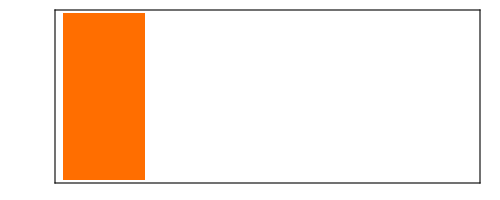
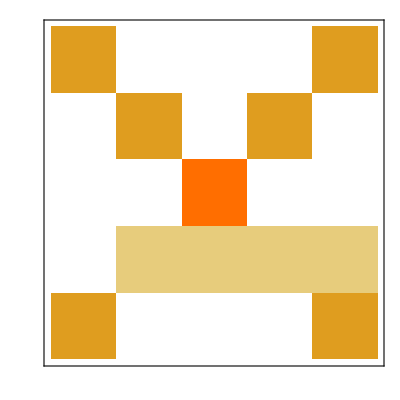
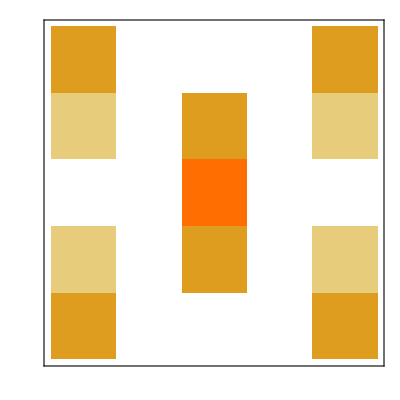
Basic Properties | 
InitialProbabilities | -Graphics-
TransitionMatrix | -Graphics-
HoldingTimeMean | {1.,1.,∞,0.333333,1.}
HoldingTimeVariance | {2.,2.,∞,0.444444,2.}
Structural Properties | 
CommunicatingClasses | {1,5}, {3}, {2,4}
RecurrentClasses | {1,5}, {3}
TransientClasses | {2,4}
AbsorbingClasses | {3}
PeriodicClasses | None
Periods | {}
Irreducible | False
Primitive | False
Aperiodic | True
Transient Properties | 
TransientVisitMean | {0.,0.}
TransientVisitVariance | {0.,0.}
TransientTotalVisitMean | 0.
Limiting Properties | 
ReachabilityProbability | {1.,0.,0.,0.,1.}
LimitTransitionMatrix | -Graphics-
Reversible | False

```mathematica
MarkovProcessProperties[pr]
```

```mathematica
p=({{.5, 0, 0, 0, .5}, {0, .5, 0, .5, 0}, {0, 0, 1, 0, 0}, {0, .25, .25, .25, .25}, {.5, 0, 0, 0, .5}})
```

{{0.5,0,0,0,0.5},{0,0.5,0,0.5,0},{0,0,1,0,0},{0,0.25,0.25,0.25,0.25},{0.5,0,0,0,0.5}}

```mathematica
Eigensystem[p]
```

{{1.,1.,0.75,2.13454×10^-9,-2.13454×10^-9},{{-0.632456,-0.316228,0.,-0.316228,-0.632456},{-0.231197,0.304876,0.84095,0.304876,-0.231197},{7.45408×10^-16,-0.894427,0.,-0.447214,4.19292×10^-16},{-9.0561×10^-9,-0.707107,0.,0.707107,9.0561×10^-9},{-9.0561×10^-9,0.707107,0.,-0.707107,9.0561×10^-9}}}

```mathematica
Inverse[Transpose[Eigenvectors[p]]]~Round~.001//MatrixForm
```

(-0.791 | 0. | -0.435 | 0. | -0.791
0. | 0. | 1.189 | 0. | 0.
0.497 | -0.745 | 0.745 | -0.745 | 0.248
-2.76057×10^7 | -0.236 | -0.118 | 0.471 | 2.76057×10^7
-2.76057×10^7 | 0.236 | 0.118 | -0.471 | 2.76057×10^7)

```mathematica
%19[[1]].p
```

{-0.791,0.,-0.435,0.,-0.791}

```mathematica
{-0.8,0.,-0.4,0.,-0.8}.p
```

{-0.8,0.,-0.4,0.,-0.8}

```mathematica
(.6^2)Sum[(.6*.4)^i,{i,0,∞}]
```

0.473684

```mathematica
9/19
```

```mathematica
9/19//N
```

0.473684

```mathematica
0.6631578947368422//Rationalize
```

63/95

```mathematica
.4*.6^2Sum[(.6*.4)^i,{i,0,∞}]
```

```mathematica
0.18947368421052632//Rationalize
```

18/95

```mathematica
pk=DiscreteMarkovProcess[1,1/25({{0, 25, 0, 0, 0}, {1, 8, 16, .5, 0}, {0, 9, 12, 4, 0}, {0, 0, 16, 8, 1}, {0, 0, 0, 25, 0}})]
```

DiscreteMarkovProcess[1,{{0,1,0,0,0},{0.0392157,0.313725,0.627451,0.0196078,0.},{0,9/25,12/25,4/25,0},{0,0,16/25,8/25,1/25},{0,0,0,1,0}}]

```mathematica
Graph[pk]
```

-Graphics-

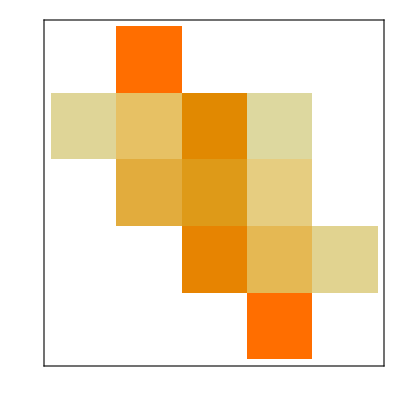
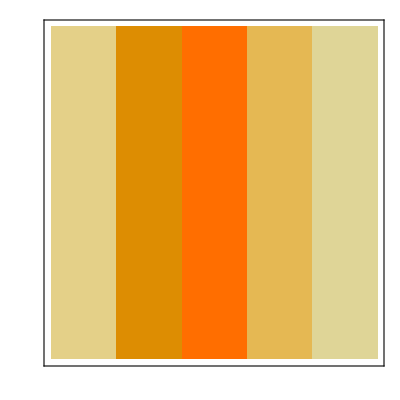
Basic Properties | 
InitialProbabilities | -Graphics-
TransitionMatrix | -Graphics-
HoldingTimeMean | {0,0.457143,12/13,8/17,0}
HoldingTimeVariance | {0,0.666122,300/169,200/289,0}
Structural Properties | 
CommunicatingClasses | {1,…,5}
RecurrentClasses | {1,…,5}
TransientClasses | None
AbsorbingClasses | None
PeriodicClasses | None
Periods | {}
Irreducible | True
Primitive | True
Aperiodic | True
Limiting Properties | 
LimitTransitionMatrix | -Graphics-
Reversible | False

```mathematica
MarkovProcessProperties[pk]
```

```mathematica
8/25//N
```

0.32

```mathematica
RowReduce[({{0, 25, 0, 0, 0}, {1, 8, 16, .5, 0}, {0, 9, 12, 4, 0}, {0, 0, 16, 8, 1}, {0, 0, 0, 25, 0}})]//MatrixForm
```

(1 | 0. | 0. | 0. | 0.
0 | 1 | 0. | 0. | 0.
0 | 0 | 1 | 0. | 0.
0 | 0 | 0 | 1 | 0.
0 | 0 | 0 | 0 | 1)

```mathematica
pl={{.5,.25,.25},{.5,0,.5},{.25,.25,.5}}
```

{{0.5,0.25,0.25},{0.5,0,0.5},{0.25,0.25,0.5}}

```mathematica
MatrixForm[pl]
```

```mathematica
Solve[{0.6 p1+0.1 p2+p3/3,0.1 p1+0.7 p2+p3/3,0.3 p1+0.3 p2+p3/3}=={p1,p2,p3},{p1,p2,p3}]
```

{{p1→0.,p2→0.,p3→0.}}

```mathematica
First[{{p1->0.,p2->0.,p3->0.}}]
```

{p1→0.,p2→0.,p3→0.}

```mathematica
pi={p1,p2,p3}.Inverse[{{0.6,0.1,0.3},{0.1,0.7,0.3},{0.2,0.2,0.6}}]//Chop
```

{2. p1-0.666667 p3,1.66667 p2-0.555556 p3,-1. p1-0.833333 p2+2.27778 p3}

```mathematica
NSolve[pi.Transpose[{pi}]==1,{p1,p2,p3}]//MatrixForm
```

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with 171802\ p1/178835 - 113492\ p2/178835 - 121484\ p3/178835 == 1.

NSolve::infsolns: Infinite solution set has dimension at least 2. Returning intersection of solutions with -159931\ p1/127051 - 145789\ p2/127051 + 152414\ p3/127051 == 1.

(p1→-0.320545-0.702627 ⅈ | p2→-1.28131-0.135592 ⅈ | p3→-0.728381-0.866978 ⅈ
p1→-0.320545+0.702627 ⅈ | p2→-1.28131+0.135592 ⅈ | p3→-0.728381+0.866978 ⅈ)

```mathematica
{{2.,0.,-1.},{0.,1.666666666666667,-0.8333333333333334},{-0.6666666666666666,-0.5555555555555557,2.2777777777777777}}
```

```mathematica
Det[{{0.6,0.1,0.3},{0.1,0.7,0.3},{0.2,0.2,0.6}}]
```

0.18

p1

```mathematica
pl
```

```mathematica
{p1,p2,p3}.{{0.6,0.1,0.3},{0.1,0.7,0.3},{0.2,0.2,0.6}}
```

```mathematica
{0.6 p1+0.1 p2+0.2 p3,0.1 p1+0.7 p2+0.2 p3,0.3 p1+0.3 p2+0.6 p3}//MatrixForm
```

```mathematica
LinearSolve[({{0.6 p1+0.1 p2+0.2 p3}, {0.1 p1+0.7 p2+0.2 p3}, {0.3 p1+0.3 p2+0.6 p3}})=={p1,p2,p3},{p1,p2,p3}]
```

```mathematica
Solve[{0.6 p1+0.1 p2+0.2 p3==p1,0.1 p1+0.7 p2+0.2 p3==p2,0.3 p1+0.3 p2+0.6 p3==p3},{p1,p2,p3}]
```

{{p1→0.,p2→0.,p3→0.}}

```mathematica
Solve[{{p1,p2,p3}.pl=={p1,p2,p3},p1+p2+p3==1}]
```

{{p1→0.4,p2→0.2,p3→0.4}}

```mathematica
pl//MatrixForm
```

(0.5 | 0.25 | 0.25
0.5 | 0 | 0.5
0.25 | 0.25 | 0.5)

```mathematica
pm={{0.5,0.25,0.25},{0.5,0,0.5},{1,1,1}}
```

{{0.5,0.25,0.25},{0.5,0,0.5},{1,1,1}}

```mathematica
Solve[{p1,p2,p3,p4,p5}.({{0, 25, 0, 0, 1}, {1, 8, 16, .5, 1}, {0, 9, 12, 4, 1}, {0, 0, 16, 8, 1}, {0, 0, 0, 25, 1}})=={p1,p2,p3,p4,1}]
```

{{p1→0.4,p2→0.2,p3→0.4}}

```mathematica
pl//MatrixForm
```

```mathematica
({{0.5, 0.25, 1}, {0.5, 0, 1}, {0.25, 0.25, 1}})
```

```mathematica
TableForm[{{0.5,0.25,0.25},{0.5,0,0.5},{0.25,0.25,0.5}}]
```

0.5 | 0.25 | 0.25
0.5 | 0 | 0.5
0.25 | 0.25 | 0.5

```mathematica
Solve[1/25{p0,p1,p2,p3,p4,p5}.{{0,25,0,0,0,25},{1,8,16,0,0,25},{0,4,12,9,0,25},
{0,0,9,12,4,25},{0,0,0,16,8,25},{0,0,0,0,25,25}}=={p0,p1,p2,p3,p4,1}]
```

{{p0→1/252,p1→25/252,p2→25/63,p3→25/63,p4→25/252,p5→1/252}}

```mathematica
{{p0->1/252,p1->25/252,p2->25/63,p3->25/63,p4->25/252,p5->1/252}}
```

```mathematica
1/25{{0,25,0,0,0,25},{1,8,16,0,0,25},{0,4,12,9,0,25},
{0,0,9,12,4,25},{0,0,0,16,8,25},{0,0,0,0,25,25}}//MatrixForm
```

```mathematica
{p0,p1,p2,p3,p4,p5}.({{0, 1, 0, 0, 0, 1}, {1/25, 8/25, 16/25, 0, 0, 1}, {0, 4/25, 12/25, 9/25, 0, 1}, {0, 0, 9/25, 12/25, 4/25, 1}, {0, 0, 0, 16/25, 8/25, 1}, {0, 0, 0, 0, 1, 1}})//MatrixForm
```

(p1/25
p0+(8 p1)/25+(4 p2)/25
(16 p1)/25+(12 p2)/25+(9 p3)/25
(9 p2)/25+(12 p3)/25+(16 p4)/25
(4 p3)/25+(8 p4)/25+p5
p0+p1+p2+p3+p4+p5)

```mathematica
Solve[{{p0,p1,p2,p3,p4,p5}.({{0, 1, 0, 0, 0, 0}, {1/25, 8/25, 16/25, 0, 0, 0}, {0, 4/25, 12/25, 9/25, 0, 0}, {0, 0, 9/25, 12/25, 4/25, 0}, {0, 0, 0, 16/25, 8/25, 1/25}, {0, 0, 0, 0, 1, 0}})=={p0,p1,p2,p3,p4,p5},Total[{p0,p1,p2,p3,p4,p5}]==1}]
```

{{p0→1/252,p1→25/252,p2→25/63,p3→25/63,p4→25/252,p5→1/252}}

```mathematica
MatrixPower[({{0, 1, 0, 0, 0, 0}, {1/25, 8/25, 16/25, 0, 0, 0}, {0, 4/25, 12/25, 9/25, 0, 0}, {0, 0, 9/25, 12/25, 4/25, 0}, {0, 0, 0, 16/25, 8/25, 1/25}, {0, 0, 0, 0, 1, 0}})//N,100]
```

{{0.00396825,0.0992063,0.396825,0.396825,0.0992063,0.00396825},{0.00396825,0.0992063,0.396825,0.396825,0.0992063,0.00396825},{0.00396825,0.0992063,0.396825,0.396825,0.0992063,0.00396825},{0.00396825,0.0992063,0.396825,0.396825,0.0992063,0.00396825},{0.00396825,0.0992063,0.396825,0.396825,0.0992063,0.00396825},{0.00396825,0.0992063,0.396825,0.396825,0.0992063,0.00396825}}

```mathematica
{1/252,25/252,25/63,25/63,25/252,1/252}//N
```

{0.00396825,0.0992063,0.396825,0.396825,0.0992063,0.00396825}

```mathematica
Total[{p0,p1,p2,p3,p4,p5}]
```

p0+p1+p2+p3+p4+p5

```mathematica
Solve[{p0,p1,p2,p3,p4,p5}.({{0, 1, 0, 0, 0, 1}, {1/25, 8/25, 16/25, 0, 0, 1}, {0, 4/25, 12/25, 9/25, 0, 1}, {0, 0, 9/25, 12/25, 4/25, 1}, {0, 0, 0, 16/25, 8/25, 1}, {0, 0, 0, 0, 1, 1}})=={p0,p1,p2,p3,p4,1}]
```

```mathematica
{{p0->1/252,p1->25/252,p2->25/63,p3->25/63,p4->25/252,p5->1/252}}//N
```

{{p0→0.00396825,p1→0.0992063,p2→0.396825,p3→0.396825,p4→0.0992063,p5→0.00396825}}

```mathematica
Total[{1/252,25/252,25/63,25/63,25/252,1/252}]
```

1

```mathematica
{{1/3,2/3,0,0,0},{1/3,0,2/3,0,0},{1/3,0,0,2/3,0},{1/3,0,0,0,2/3},{1,.0,0,0,0}}~MatrixPower~10000//MatrixForm
```

```mathematica
({{0.383886255924071, 0.2559241706160474, 0.17061611374403157, 0.11374407582935438, 0.07582938388623625}, {0.383886255924071, 0.2559241706160474, 0.17061611374403157, 0.11374407582935438, 0.07582938388623625}, {0.383886255924071, 0.2559241706160474, 0.17061611374403157, 0.11374407582935438, 0.07582938388623625}, {0.38388625592407105, 0.25592417061604744, 0.17061611374403157, 0.11374407582935438, 0.07582938388623627}, {0.383886255924071, 0.2559241706160474, 0.17061611374403157, 0.11374407582935438, 0.07582938388623625}})~Round~.01
```

```mathematica
{{0.38,0.26,0.17,0.11,0.08},{0.38,0.26,0.17,0.11,0.08},{0.38,0.26,0.17,0.11,0.08},{0.38,0.26,0.17,0.11,0.08},{0.38,0.26,0.17,0.11,0.08}}//TeXForm
```

\left(
\begin{array}{ccccc}
 0.38 & 0.26 & 0.17 & 0.11 & 0.08 \\
 0.38 & 0.26 & 0.17 & 0.11 & 0.08 \\
 0.38 & 0.26 & 0.17 & 0.11 & 0.08 \\
 0.38 & 0.26 & 0.17 & 0.11 & 0.08 \\
 0.38 & 0.26 & 0.17 & 0.11 & 0.08 \\
\end{array}
\right)

```mathematica
{{0.32670000000000005,0.21780000000000002,0.43560000000000004,0.,0.},{0.32670000000000005,0.21780000000000002,0.,0.43560000000000004,0.},{0.32670000000000005,0.21780000000000002,0.,0.,0.43560000000000004},{0.7689,0.21780000000000002,0.,0.,0.},{0.33,0.66,0.,0.,0.}}//MatrixForm
```

```mathematica
({{0.32670000000000005, 0.21780000000000002, 0.43560000000000004, 0., 0.}, {0.32670000000000005, 0.21780000000000002, 0., 0.43560000000000004, 0.}, {0.32670000000000005, 0.21780000000000002, 0., 0., 0.43560000000000004}, {0.7689, 0.21780000000000002, 0., 0., 0.}, {0.33, 0.66, 0., 0., 0.}})~Round~.01
```

```mathematica
{{0.33,0.22,0.44,0.,0.},{0.33,0.22,0.,0.44,0.},{0.33,0.22,0.,0.,0.44},{0.77,0.22,0.,0.,0.},{0.33,0.66,0.,0.,0.}}//MatrixForm
```

```mathematica
{0,0,0,1,0}.({{0.33, 0.22, 0.44, 0., 0.}, {0.33, 0.22, 0., 0.44, 0.}, {0.33, 0.22, 0., 0., 0.44}, {0.77, 0.22, 0., 0., 0.}, {0.33, 0.66, 0., 0., 0.}})
```

{0.77,0.22,0.,0.,0.}